```mathematica
psi0=Transpose[{{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}];
Rxa={{Cos[thetaA/2],-I Sin[thetaA/2]},{-I Sin[thetaA/2],Cos[thetaA/2]}};
Rxb={{Cos[thetaB/2],-I Sin[thetaB/2]},{-I Sin[thetaB/2],Cos[thetaB/2]}};
rotation=KroneckerProduct[Rxa,IdentityMatrix[4],Rxb];
cnot01={{1,0,0,0},{0,1,0,0},{0,0,0,1},{0,0,1,0}};
cnot10={{1,0,0,0},{0,0,0,1},{0,0,1,0},{0,1,0,0}};
cnots=KroneckerProduct[cnot01,cnot10];
therma=cnots.rotation.psi0;
psit=FullSimplify[therma.ConjugateTranspose[therma],{thetaA>0&& thetaB>0}];
psif=ResourceFunction["MatrixPartialTrace"][psit,{2,3},2]//MatrixForm
(*psif=(1/(Za*Zb))*{{Exp[-((ba*ea)/2)-((bb*eb)/2)],0,0,0},{0,Exp[((bb*eb)/2)-((ba*ea)/2)],0,0},{0,0,Exp[((ba*ea)/2)-((bb*eb)/2)],0},{0,0,0,Exp[((ba*ea)/2)+((bb*eb)/2)]}};
Za=Tr[MatrixExp[-ba*ea*PauliMatrix[3]/2]];
Zb=Tr[MatrixExp[-bb*eb*PauliMatrix[3]/2]];*)
(*Clear[a,b,c,d];
psif={{a,0,0,0},{0,b,0,0},{0,0,c,0},{0,0,0,d}}*)
```

(Cos[thetaA/2]^2 Cos[thetaB/2]^2 | 0 | 0 | 0
0 | Cos[thetaA/2]^2 Sin[thetaB/2]^2 | 0 | 0
0 | 0 | Cos[thetaB/2]^2 Sin[thetaA/2]^2 | 0
0 | 0 | 0 | Sin[thetaA/2]^2 Sin[thetaB/2]^2)

```mathematica
Clear[θ,ϕ]
(*a=f*g;
b=f*(1-g);
c=g*(1-f);
d=(1-g)*(1-f);*)
psif={{a,0,0,0},{0,b,0,0},{0,0,c,0},{0,0,0,d}}
ry1={{Cos[(θ+ϕ)/2],-Sin[(θ+ϕ)/2]},{Sin[(θ+ϕ)/2],Cos[(θ+ϕ)/2]}};
ry11=KroneckerProduct[ry1,IdentityMatrix[2]];
ry2={{Cos[(θ-ϕ)/2],-Sin[(θ-ϕ)/2]},{Sin[(θ-ϕ)/2],Cos[(θ-ϕ)/2]}};
ry22=KroneckerProduct[ry2,IdentityMatrix[2]];
u=cnot01.ry22.cnot10.ry11;
psix=Simplify[u.psif.ConjugateTranspose[u],{θ>0&&ϕ>0}]//MatrixForm
```

{{a,0,0,0},{0,b,0,0},{0,0,c,0},{0,0,0,d}}

(a Cos[θ]^2+c Sin[θ]^2 | 0 | 0 | (a-c) Cos[θ] Sin[θ]
0 | d Cos[ϕ]^2+b Sin[ϕ]^2 | (b-d) Cos[ϕ] Sin[ϕ] | 0
0 | (b-d) Cos[ϕ] Sin[ϕ] | b Cos[ϕ]^2+d Sin[ϕ]^2 | 0
(a-c) Cos[θ] Sin[θ] | 0 | 0 | c Cos[θ]^2+a Sin[θ]^2)

```mathematica
ps1=Simplify[ResourceFunction["DiagonalizeMatrix"][u.psif.ConjugateTranspose[u]],{θ>0&&ϕ>0}];
Simplify[Tr[ps1]]
```

1

```mathematica
Za=Tr[MatrixExp[-ba*ea*PauliMatrix[3]/2]];
Zb=Tr[MatrixExp[-bb*eb*PauliMatrix[3]/2]];
a=Exp[(-ea*ba-eb*bb)/2]/(Za*Zb);
b=Exp[(-ea*ba+eb*bb)/2]/(Za*Zb)
c=Exp[(ea*ba-eb*bb)/2]/(Za*Zb)
d=Exp[(ea*ba+eb*bb)/2]/(Za*Zb);
w=1/(Za*Zb);
z=1/(Za*Zb);
θ=1/2 ArcTan[(2*w)/(a-d)]
p00=(a*Cos[θ]^2-d*Sin[θ]^2)/Cos[2*θ];
p10=(-a*Sin[θ]^2+d*Cos[θ]^2)/Cos[2*θ];
ϕ=1/2 ArcTan[(2*z)/(b-c)]
p01=(b*Cos[ϕ]^2-c*Sin[ϕ]^2)/Cos[2*ϕ];
p11=(-b*Sin[ϕ]^2+c*Cos[ϕ]^2)/Cos[2*ϕ];
```

```mathematica
Solve[{j==((2pp*pm-pp)*g),k==((2*pm-2*pm*pp+pp-1)*h)},{pm,pp}]
```

{{pm→(g h+h j+g k)/(2 g h),pp→(h j)/(h j+g k)}}

Solve::naqs: eqn1&&eqn2&&eqn3&&eqn4&&eqn5&&eqn6 is not a quantified system of equations and inequalities.

Solve[{eqn1,eqn2,eqn3,eqn4,eqn5,eqn6},{θ,ϕ,p01,p00,p10,p11}]

```mathematica
Simplify[(Exp[(-ea*ba-bb*ea)/2]+Exp[(ea*ba+bb*ea)/2])]
```

```mathematica
Clear[ea,ba,bb,eb]
```

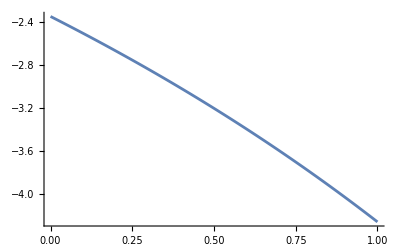

```mathematica
Plot[((Exp[(-ea*ba-bb*eb)/2]-Exp[(ea*ba+bb*eb)/2])),{ea,0,1}]
```

```mathematica
Clear[a,b]
eqn1=p00==a*b;
eqn2=p10==a*(1-b);
eqn3=p01==(1-a)*b;
eqn4=p11==(1-a)*(1-b);
```

```mathematica
sol=Solve[{eqn1,eqn2,eqn3,eqn4},{a,b}]
```

{}

```mathematica
Clear[gamma,x]
(*x=1/2*(1+Sqrt[1-4*alpha^2/(pa-pb)^2]);*)
FullSimplify[Solve[{(1-pa)*pb==1/4 (-xa(xb + 2 x - 1) + (2 x - 1)xb + 1),pa*(1-pb)==1/4 (-xa (xb-2x+1)-2x*xb+xb+1)},{xa,xb}]]
```

{{xa→(pa-pb+√((-1+pa+pb)^2-4 (-1+2 pa) (-1+2 pb) x+4 (-1+2 pa) (-1+2 pb) x^2))/(-1+2 x),xb→(-pa+pb+√((-1+pa+pb)^2-4 (-1+2 pa) (-1+2 pb) x+4 (-1+2 pa) (-1+2 pb) x^2))/(-1+2 x)},{xa→(-pa+pb+√((pa-pb)^2+(-1+2 pa) (-1+2 pb) (1-2 x)^2))/(1-2 x),xb→-(pa-pb+√((-1+pa+pb)^2-4 (-1+2 pa) (-1+2 pb) x+4 (-1+2 pa) (-1+2 pb) x^2))/(-1+2 x)}}